# ConfusionMatrixPlot

## Background

一个简单的电商图像分类模型，数据量在一万张左右，33个三级类目，常见的包包，手机壳，化妆品等。

故事：好久前把GPU测试机器装好后，下了点数据集就怒练了一下，遇到两个问题，一是验证集准确度0.45...，二是还有Ubuntu系统中，Mma内存中加载图片多时，代码写得随意会有处理时会有卡顿的情况。然后就没有然后了，当时还没以为是训练效果不好，忙别的去了。

这几天在整理数据集，把代码Refresh了一下，对Ubuntu下的数据预处理部分的代码优化了一下，不会出现卡顿情况。
另外因为样本不平衡的情况，想10分钟内搞定训练，就导致验证集有的类目中有许多图片，而11.3的ClassifierMeausurement有一个Bug就是GPU选项不生效。。。[我也是被网友提醒才发现，因为11.1开始就嫌弃速度太慢了，常使用自己DIY的使用GPU的评价函数。
我想说——坑爹的Mma，这个是一个新功能啊，结果是个Bug。。。加上最近新上了几块1080卡，发现多GPU的训练的问题。。。又是坑爹]
跑题了，总之，Mma想干点正经事情都会有许多奇怪的问题

在这个数据集中，类目ID相似的或连续的，极可能是非常相似的，经过今天的验证，其实精度没有那么差。

## Evaluation

#### SampleEvaluation@Accuracy@GPU

```mathematica
eval[model_,dataSets_,prob_:0.5]:=Block[{(*res,*)lengthT,length,acc},
res=Transpose[{dataSets[[All,2]],model[dataSets[[All,1]],TargetDevice->"CPU"]}];
lengthT=Length@Select[res,#[[1]]==#[[2]]&];
length=Length@dataSets;
acc=lengthT/length//N
]
```

```mathematica
eval1[model_,dataSets_Rule,prob_:0.5]:=Block[{res,lengthT,length,acc},
res=Transpose[{dataSets[[2]],model[dataSets[[1]],TargetDevice->"GPU"]}];
lengthT=Length@Select[res,#[[1]]==#[[2]]&];
length=Length@dataSets[[2]];
acc=lengthT/length//N
]
```

## ConfusionMatrixGeneration

```mathematica
classIndex=AssociationThread[classes->Range[Length@classes]];
```

```mathematica
matrix=SparseArray@Normal@KeyMap[Map[classIndex,#,{1}]&,Counts[res]]
```

## Test@MNIST

```mathematica
c=Classify[{
-Graphics-->6,-Graphics-->0,-Graphics-->5,-Graphics-->7,-Graphics-->1,-Graphics-->3,-Graphics-->2,-Graphics-->0,-Graphics-->3,-Graphics-->5,-Graphics-->8,-Graphics-->2,-Graphics-->9,-Graphics-->8,-Graphics-->8,-Graphics-->9,-Graphics-->5,-Graphics-->4,-Graphics-->4,-Graphics-->7,-Graphics-->2,-Graphics-->3,-Graphics-->1,-Graphics-->4,-Graphics-->0,-Graphics-->9,-Graphics-->8,-Graphics-->6,-Graphics-->7,-Graphics-->6,-Graphics-->7,-Graphics-->0,-Graphics-->6,-Graphics-->4,-Graphics-->1,-Graphics-->7,-Graphics-->2,-Graphics-->9,-Graphics-->4,-Graphics-->0,-Graphics-->1,-Graphics-->9,-Graphics-->5,-Graphics-->9,-Graphics-->6,-Graphics-->9,-Graphics-->2,-Graphics-->5,-Graphics-->6,-Graphics-->8,-Graphics-->6,-Graphics-->4,-Graphics-->9,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->0,-Graphics-->0,-Graphics-->7,-Graphics-->4,-Graphics-->8,-Graphics-->4,-Graphics-->2,-Graphics-->5,-Graphics-->7,-Graphics-->5,-Graphics-->1,-Graphics-->5,-Graphics-->3,-Graphics-->0,-Graphics-->6,-Graphics-->3,-Graphics-->3,-Graphics-->6,-Graphics-->7,-Graphics-->9,-Graphics-->3,-Graphics-->4,-Graphics-->9,-Graphics-->0,-Graphics-->8,-Graphics-->2,-Graphics-->8,-Graphics-->1,-Graphics-->2,-Graphics-->5,-Graphics-->6,-Graphics-->5,-Graphics-->3,-Graphics-->1,-Graphics-->4,-Graphics-->7,-Graphics-->0,-Graphics-->2,-Graphics-->8,-Graphics-->3,-Graphics-->8,-Graphics-->7,-Graphics-->3,-Graphics-->1}]
```

ClassifierFunction[…]

Generate a ClassifierMeasurementsObjectpaclet:ref/ClassifierMeasurementsObject of the classifier on the MNIST test set:

```mathematica
cm=ClassifierMeasurements[c,data=ExampleData[{"MachineLearning","MNIST"},"TestData"]]
```

ClassifierMeasurementsObject[…]

Visualize the confusion matrix:

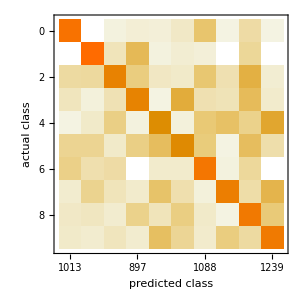

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
eval[c,data]
```

0.7365

```mathematica
classes=data[[All,-1]]//Union
classIndex=AssociationThread[classes->Range[Length@classes]];
matrix=SparseArray@Normal@KeyMap[Map[classIndex,#,{1}]&,Counts[res]]
```

{0,1,2,3,4,5,6,7,8,9}

SparseArray[…]

## ConfusionMatrixPlot

```mathematica
<<"/Users/hypergroups/Nustore Files/temp_1/matrixPlot.1.mx"
```

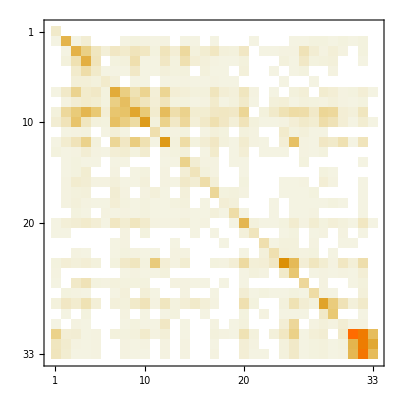

```mathematica
MatrixPlot[matrix,PlotRange->All]
```

```mathematica
m=Normal@matrix;
```

```mathematica
<<"/Users/hypergroups/Nustore Files/temp_1/classIndex.mx"
```

```mathematica
classIndexReverse=AssociationMap[Reverse,classIndex]
```

<|1→1011,2→1084,3→1088,4→1090,5→1091,6→1092,7→1093,8→1095,9→1096,10→1097,11→1098,12→1100,13→1101,14→1103,15→1106,16→1108,17→1113,18→1115,19→1117,20→1131,21→1132,22→1134,23→1135,24→1136,25→1137,26→1138,27→1140,28→1143,29→1144,30→1145,31→1179,32→1180,33→1181|>

```mathematica
classes=Values@classIndexReverse
```

{1011,1084,1088,1090,1091,1092,1093,1095,1096,1097,1098,1100,1101,1103,1106,1108,1113,1115,1117,1131,1132,1134,1135,1136,1137,1138,1140,1143,1144,1145,1179,1180,1181}

```mathematica
t=Transpose@Map[Flatten,{#,Reverse@Transpose@#}&[Table[Range[1,2 #-1,2],{#}]]&[Length@m]]/2;
```

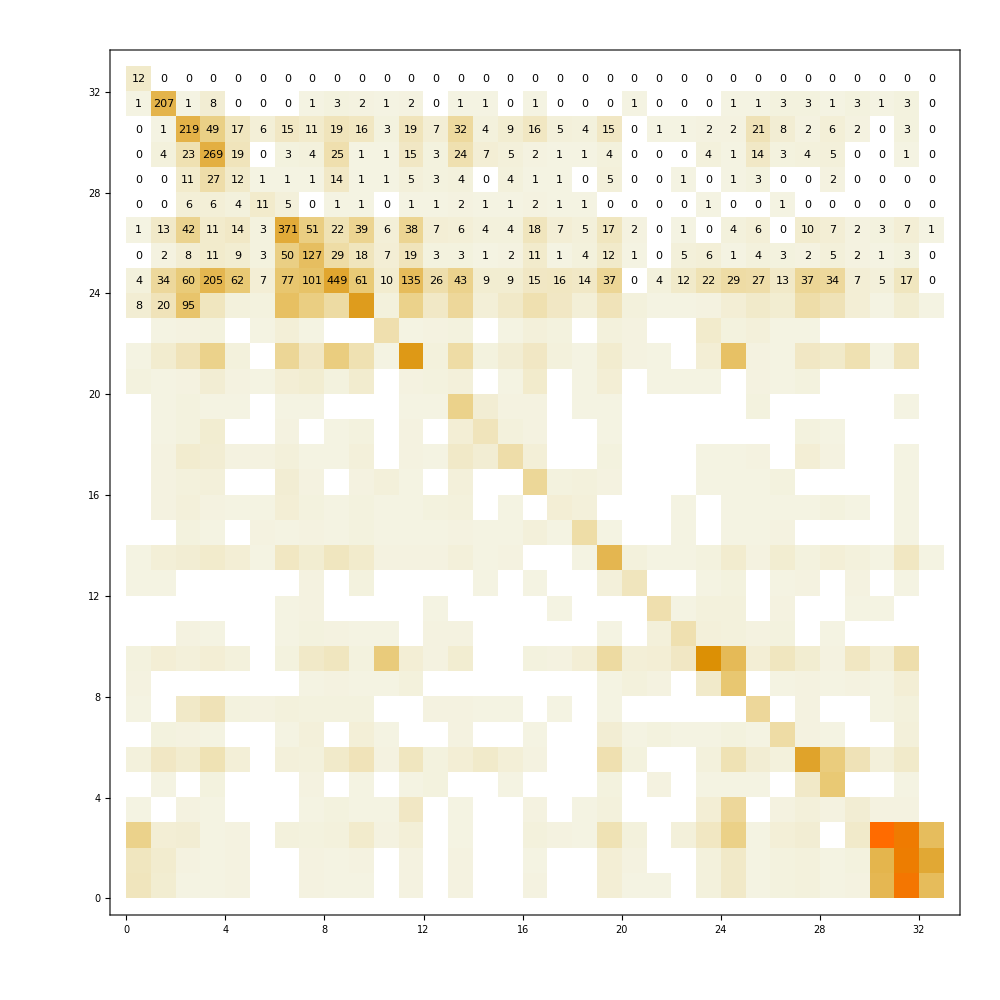

```mathematica
MatrixPlot[m,Epilog->Text@@@Transpose[{Catenate@m,t}],FrameTicks->{List@@@Normal@classIndexReverse,List@@@Normal@classIndexReverse,List@@@Normal@classIndexReverse,List@@@Normal@classIndexReverse},ImageSize->1000]
```

## Summary

### 项目小结

模型本身没有大的问题，左上角一坨和右下角三个类目本身比较相似，暂时在解决更重要数据问题前也不用调什么参数优化。

右下角的这种连续的类目ID经过我人工查看，确实是相似或相同的东西，1011是手机壳，1179-1180-1181则是钱包，这两个东西确实比较像。
优化：增加类目样本及精准度，Merge相似类目，使用上级类目或多级MultiTask训练

### 文章小结

有些DIY的函数，优化的小代码，大家有兴趣的可以多写写，整合整合。
只能希望12.0把一些严重bug修复一下。。。希望功能稳定点，可以少花点时间折腾吧

本文主要是今天增加了个小功能，图像分类模板文件已经传到GitHub，后续把以前的几个模板再整合整合再更新，有兴趣的可以多玩玩。

## Refs

question@plot

problem@MultiGPUs

problem@ParallelInference@MultiCPUsGPUs@没什么效果。。。